## Data Preparation

```mathematica
SetDirectory["C:/Users/nchil/Downloads/Research/Chiles_Bloom_Filter"]
```

C:\Users\nchil\Downloads\Research\Chiles_Bloom_Filter

#### HIV

```mathematica
hiv=Import["HIV.csv","Dataset",HeaderLines->1];
hivtable=Normal@hiv[GroupBy["HIV_active"],All,"smiles"];
actHIVmol=Molecule/@hivtable[1];
inactHIVmol=Molecule/@hivtable[0][[1;;1487]];
(* 1487 examples each of active/inactive *)
actHIV=SparseArray/@FeatureExtract[actHIVmol,"MoleculeExtendedConnectivity"] ;(* bit vectors locally*)
inactHIV=SparseArray/@FeatureExtract[inactHIVmol,"MoleculeExtendedConnectivity"] ;
```

#### Mu

```mathematica
actMu=Get["mu_active.mx"];
inactMu=Get["mu_inactive.mx"];
```

#### Tox

```mathematica
d2=Import["tox21.csv.gz","Dataset",HeaderLines->1];
nrar=Normal@d2[GroupBy["NR-AR"],All,"smiles"];
t=Molecule/@nrar[[3]];
nont=Molecule/@nrar[[1]];
tox=SparseArray/@FeatureExtract[t,"MoleculeExtendedConnectivity"];
nontox=SparseArray/@FeatureExtract[nont,"MoleculeExtendedConnectivity"];
```

#### HIV Dataset

```mathematica
SetDirectory@NotebookDirectory[];
<< "fruit fly functions.wl"
```

```mathematica
SeedRandom[2000];
```

```mathematica
fly1={pos[actHIV,inactHIV][20,500,50],neg[actHIV,inactHIV][20,500,50]};
```

```mathematica
dt1=classStats["DecisionTree",actHIV,inactHIV][20,500,50];
rf1=classStats["RandomForest",actHIV,inactHIV][20,500,50];
lr1=classStats["LogisticRegression",actHIV,inactHIV][20,500,50];
nn1=classStats["NearestNeighbors",actHIV,inactHIV][20,500,50];
```

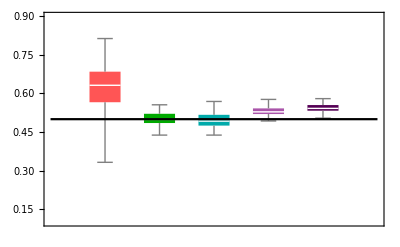

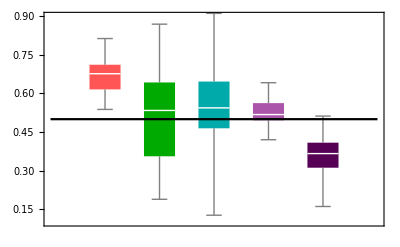

```mathematica
accHIV=accChart[fly1,dt1,rf1,lr1,nn1];
recHIV=recChart[fly1,dt1,rf1,lr1,nn1];
a1=Show[accHIV,horiz]
a2=Show[recHIV,horiz]
```

F1 score might be a better measure of performance across classifiers...

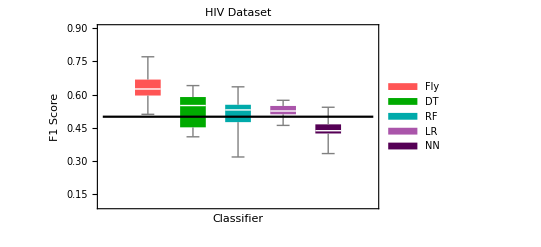

```mathematica
(* a3=Show[BoxWhiskerChart[
F1HIV,
ChartStyle->{Lighter[Red],Darker[Green],Darker[Cyan],Lighter[Purple],Darker[Purple]},
PlotLabel->"HIV Dataset",
LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold},
PlotRange->{0.1,0.9},
ChartLegends->Placed[{"Fly","DT","RF","LR","NN"},Right],
FrameLabel->{"Classifier","F1 Score"}],horiz] *)
```

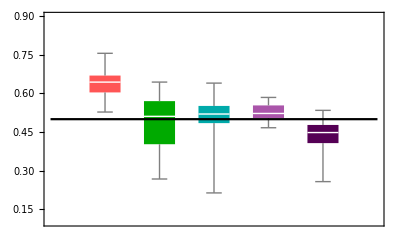

```mathematica
F1HIV=F1List[fly1,dt1,rf1,lr1,nn1];
F1GraphHIV=F1Chart[F1HIV];
a3=Show[F1GraphHIV,horiz]
```

```mathematica
(* Comparing run times -- code back in if this data is desired *)
(* bloomTime=Timing[{outHIVpos[20,100,10],outHIVneg[20,100,10]}];
lrTime=Timing[alllr[20,100,10]];
bloomTime2=Timing[{outHIVpos[20,500,20],outHIVneg[20,500,20]}];
lrTime2=Timing[alllr[20,500,20]]; *)
```

```mathematica
rowHIV=GraphicsRow[{a1,a2,a3}];
```

#### Mu Dataset

```mathematica
SeedRandom[2000];
```

```mathematica
fly2={pos[actMu,inactMu][20,500,50],neg[actMu,inactMu][20,500,50]};
```

```mathematica
dt2=classStats["DecisionTree",actMu,inactMu][20,500,50];
rf2=classStats["RandomForest",actMu,inactMu][20,500,50];
lr2=classStats["LogisticRegression",actMu,inactMu][20,500,50];
nn2=classStats["NearestNeighbors",actMu,inactMu][20,500,50];
```

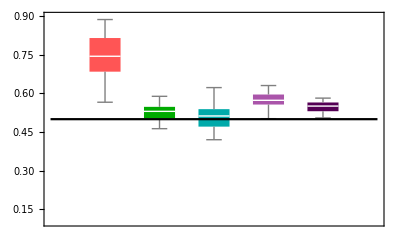

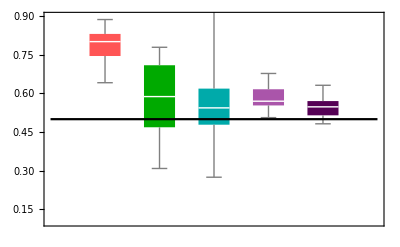

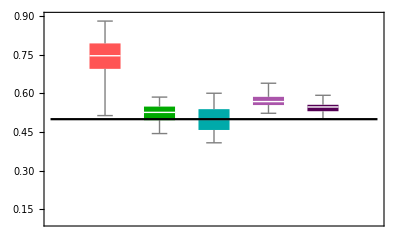

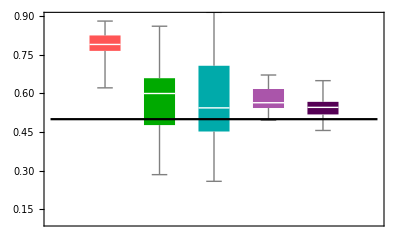

```mathematica
accMu=accChart[fly2,dt2,rf2,lr2,nn2];
recMu=recChart[fly2,dt2,rf2,lr2,nn2];
b1=Show[accMu,horiz]
b2=Show[recMu,horiz]
```

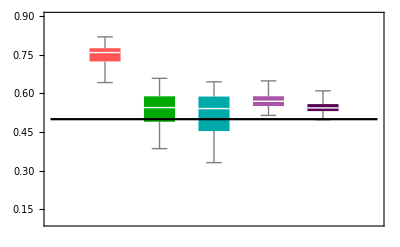

```mathematica
F1Mu=F1List[fly2,dt2,rf2,lr2,nn2];
F1GraphMu=F1Chart[F1Mu];
b3=Show[F1GraphMu,horiz]
```

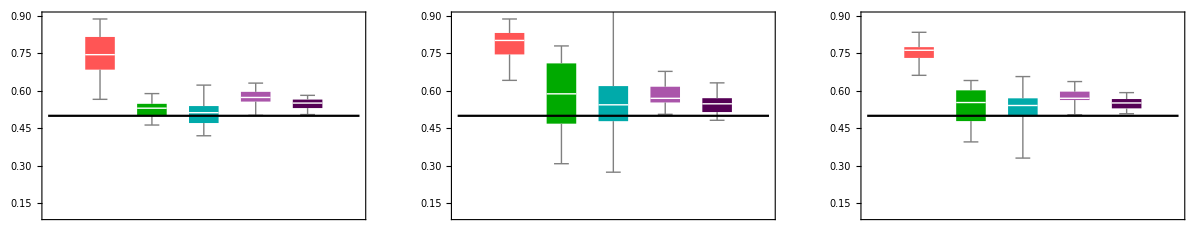

```mathematica
rowMu=GraphicsRow[{b1,b2,b3}];
```

#### Tox Dataset

```mathematica
SeedRandom[2000];
```

```mathematica
fly3={pos[tox,nontox][20,200,50],neg[tox,nontox][20,200,50]};
```

```mathematica
dt3=classStats["DecisionTree",tox,nontox][20,200,50];
rf3=classStats["RandomForest",tox,nontox][20,200,50];
lr3=classStats["LogisticRegression",tox,nontox][20,200,50];
nn3=classStats["NearestNeighbors",tox,nontox][20,200,50];
```

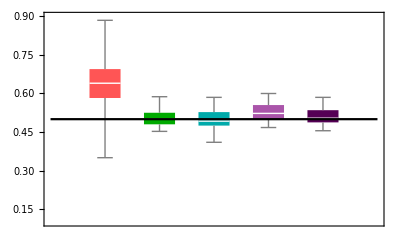

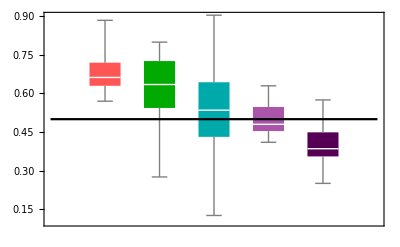

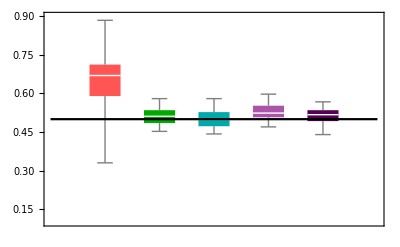

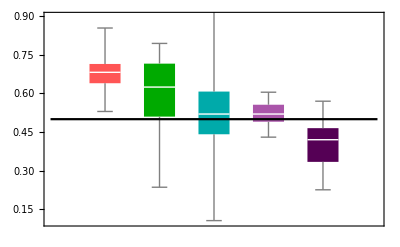

```mathematica
accTox=accChart[fly3,dt3,rf3,lr3,nn3];
recTox=recChart[fly3,dt3,rf3,lr3,nn3];
c1=Show[accTox,horiz]
c2=Show[recTox,horiz]
```

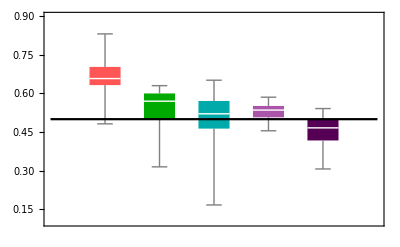

```mathematica
F1Tox=F1List[fly3,dt3,rf3,lr3,nn3];
F1GraphTox=F1Chart[F1Tox];
c3=Show[F1GraphTox,horiz]
```

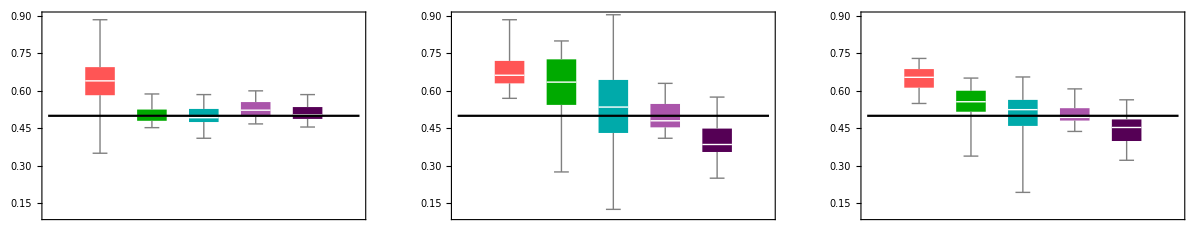

```mathematica
rowTox=GraphicsRow[{c1,c2,c3}];
```

Takeaway: The Bloom filter model consistently performs as well as traditional classifiers under low-data constraints. It also benefits from quick and simple computation.
This may not provide an alternative to accepted classifying methods in its current state but this shows promise for other applications when training data is sparse and predictions must be made with low processing power.

```mathematica
plots={{a1,a2,a3},{b1,b2,b3},{c1,c2,c3}};
xlabels=Text[Style[#,FontFamily->"Times",Large]]&/@{"","Accuracy","Recall","F1 Score"};
ylabels=Text[Style[#,FontFamily->"Times",Large]]&/@{"HIV Dataset","Mu Dataset","Tox Dataset"};
Grid[Join[{xlabels},Transpose[Join[{ylabels},Transpose[plots]]]],Spacings->{2,1}]
```

| Accuracy | Recall | F1 Score
HIV Dataset | -Graphics- | -Graphics- | -Graphics-
Mu Dataset | -Graphics- | -Graphics- | -Graphics-
Tox Dataset | -Graphics- | -Graphics- | -Graphics-

### Expanding: Different Ways of Representing Data

#### Change data skew, use balanced classification rate AS OF 12/17/2022, EVERYTHING BELOW HAS NOT BEEN CLEANED/FIXED

```mathematica
Clear[evaluateModel,boolePos,booleNeg];
evaluateModel[splitData_Association,method_String]:=With[{model=Classify[splitData["train"],Method->method]},ClassifierMeasurements[model,splitData["test"],{"Accuracy","Recall"}]]
boolePos[trainplustest_]:=Map[booleTrue,RandomSample[actHIV,trainplustest]];
booleNeg[trainplustest_]:=Map[booleFalse,RandomSample[inactHIV,trainplustest]];
```

```mathematica
lrStats[train_,testP_,testN_]:=With[{learningdata=sampleSplit2[boolePos[train+testP],booleNeg[train+testN],train]},evaluateModel[learningdata,"LogisticRegression"]]
alllr[train_,testP_,testN_,iterations_]:=ParallelTable[lrStats[train,testP,testN],iterations]//Transpose;
```

```mathematica
lrHIV=alllr[20,20,180,50];
hivBloom={outHIVpos[20,20,50],outHIVneg[20,180,50]};
```

```mathematica
(* bloom filter confusion matrix for skewed data *)
{TP,FN,FP,TN}={hivBloom[[1]],1-hivBloom[[1]],hivBloom[[2]],1-hivBloom[[2]]};
```

```mathematica
sensitivity=TP/(TP+FN);
specificity=TN/(TN+FP);
balancedAccuracy=(sensitivity+specificity)/2;
```

```mathematica
{TPlr,FNlr,FPlr,TNlr}={Table[lrHIV[[2,x,2]],{x,1,50}],
1-Table[lrHIV[[2,x,2]],{x,1,50}] ,
1-Table[lrHIV[[2,x,1]],{x,1,50}] ,
Table[lrHIV[[2,x,1]],{x,1,50}] };
```

```mathematica
sensitivitylr=TPlr/(TPlr+FNlr);
specificitylr=TNlr/(TNlr+FPlr);
balancedAccuracylr=(sensitivitylr+specificitylr)/2;
```

```mathematica
bcrHIV=BoxWhiskerChart[{balancedAccuracy,balancedAccuracylr},ChartStyle->{Lighter[Red],Lighter[Purple]},PlotLabel->"HIV Dataset",LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold},PlotRange->{0.2,0.8},ChartLegends->Placed[{"Fly","LR"},Right],FrameLabel->{"","Balanced Classification Rate"}];
```

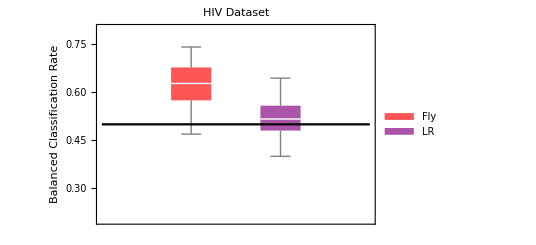

```mathematica
Show[bcrHIV,horiz]
```

```mathematica
horizBAC=Plot[0.5,{x,0,3},PlotStyle->Black];
```

Balance Accuracy Binary Classification: https://neptune.ai/blog/balanced-accuracy for reference.
For this iteration of skewed data, the bloom filter BABC was 0.637 compared with logistic regression’s 0.517. BoxWhiskerCharts look very similar between the two.

#### Learning Curve for Low Data

```mathematica
Clear[lrStats,alllr];
lrStats[train_,test_]:=With[{learningdata=sampleSplit2[boolePos[train+test],booleNeg[train+test],train]},evaluateModel[learningdata,"LogisticRegression"]];
alllr[train_,test_,iterations_]:=ParallelTable[lrStats[train,test],iterations]//Transpose;
```

```mathematica
(* 25 iterations at each n train value, test 100 *)
lrLearnCurve=Table[alllr[x,100,25],{x,1,100}];
```

```mathematica
hivBloomLearnCurve=Table[{outHIVpos[x,100,25],outHIVneg[x,100,25]},{x,1,100}];
```

```mathematica
learnListlr=Table[lrLearnCurve[[x,1]],{x,1,100}];
```

```mathematica
pos=Table[hivBloomLearnCurve[[x,1]],{x,1,100}];
neg=Table[hivBloomLearnCurve[[x,2]],{x,1,100}];
```

```mathematica
(* posMean=Mean/@pos;
negMean=Mean/@neg; *)
```

```mathematica
sums=Table[{pos[[x]],1-neg[[x]]},{x,1,100}];
learnList=Mean/@sums;
```

```mathematica
baseline=Table[.5,100];
```

```mathematica
totes=Table[Join[hivBloomLearnCurve[[x,1]],1-hivBloomLearnCurve[[x,2]]],{x,1,100}];
```

```mathematica
sd=StandardDeviation/@totes;
```

```mathematica
errorFly=MeanAround/@totes;
errorLR=MeanAround/@learnListlr;
```

```mathematica
lrLearnCurve[[1,2,1;;25,2]]
```

{0.22,0.3,0.05,0.44,0.12,0.36,0.22,0.32,0.33,0.15,0.22,0.84,0.3,0.25,0.32,0.12,0.33,0.27,0.26,0.27,0.68,0.17,0.39,0.82,0.29}

```mathematica
lrRecall=Table[lrLearnCurve[[x,2,1;;25,2]],{x,1,100}];
```

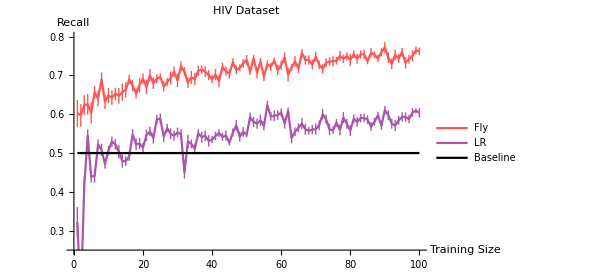

```mathematica
ListLinePlot[{MeanAround/@pos,MeanAround/@lrRecall,baseline},PlotRange->{.25,.8},PlotStyle->{Lighter[Red],Lighter[Purple],Black},PlotLabel->"HIV Dataset",LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold},PlotRange->{0.2,0.8},PlotLegends->Placed[{"Fly","LR","Baseline"},Right],AxesLabel->{"Training Size","Recall"}]
```

```mathematica
learnListlr[[1]]
```

{0.485,0.49,0.455,0.505,0.455,0.585,0.485,0.52,0.455,0.475,0.485,0.505,0.425,0.52,0.455,0.52,0.43,0.455,0.525,0.555,0.425,0.48,0.46,0.525,0.505}

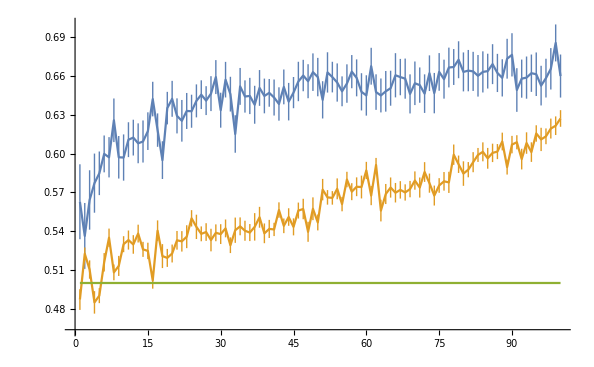

```mathematica
ListLinePlot[{errorFly,errorLR,baseline}]
```

The fly filter consistently performs ~10% more *accurately* than LR for all training values 0-50! The recall chart probably does a better job representing this.

#### Fly across more training values

```mathematica
hivBloomLearnCurveFull=Table[{outHIVpos[x,100,10],outHIVneg[x,100,10]},{x,10,1000,10}];
```

```mathematica
lrLearnCurveFull=Table[alllr[x,100,10],{x,10,1000,10}];
```

```mathematica
posFull=Table[hivBloomLearnCurveFull[[x,1]],{x,1,100}];
negFull=Table[hivBloomLearnCurveFull[[x,2]],{x,1,100}];
accFull=Transpose[{Range[10,1000,10],MeanAround/@Table[Join[posFull[[x]],1-negFull[[x]]],{x,1,100}]}];
```

```mathematica
lrAccFull=Transpose[{Range[10,1000,10],MeanAround/@Table[lrLearnCurveFull[[x,1]],{x,1,100}]}];
```

```mathematica
lrRecallFull=Table[lrLearnCurveFull[[x,2,1;;10,2]],{x,1,100}];
```

```mathematica
baseline=Table[.5,1000];
```

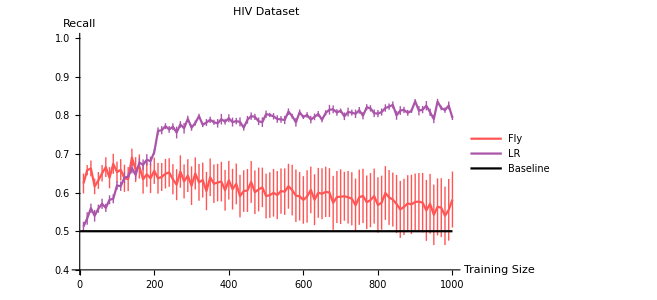

```mathematica
ListLinePlot[{accFull,lrAccFull,baseline},PlotRange->{.4,1.0},PlotStyle->{Lighter[Red],Lighter[Purple],Black},PlotLabel->"HIV Dataset",LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold},PlotLegends->Placed[{"Fly","LR","Baseline"},Right],AxesLabel->{"Training Size","Recall"}]
```

#### Adding negative weights?

```mathematica
hivBloomPos={outHIVpos[20,500,50],outHIVneg[20,500,20]};
```

```mathematica
Clear[M,projectM];
M[size_:2000,numberOfBits_:6,inputLength_:2048]:=Table[RandomSample[Join[Table[1,numberOfBits/2],Table[-1,numberOfBits/2],Table[0,size-numberOfBits]]],inputLength];
projectM[statRandM_][traindata_,m_:2000,k_:25]:=ReplacePart[Table[1,m],#->0&/@Ordering[Abs[traindata.statRandM],-k]];
```

```mathematica
(* this takes a little while to run *)
hivBloomNeg={outHIVpos[20,100,10],outHIVneg[20,100,10]};
```

```mathematica
{negTP,negFN,negFP,negTN}={hivBloomNeg[[1]],1-hivBloomNeg[[1]],hivBloomNeg[[2]],1-hivBloomNeg[[2]]};
```

```mathematica
F1BloomNeg=negTP/(negTP+.5(negFP+negFN));
```

```mathematica
F1HIVNeg=BoxWhiskerChart[{F1Bloom,F1BloomNeg,F1lr},ChartStyle->{Lighter[Red],Darker[Red],Lighter[Purple]},PlotLabel->"HIV Dataset",LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold},PlotRange->{0.1,0.9},ChartLegends->Placed[{"Fly Pos","Fly Neg","LR"},Right],FrameLabel->{"","F1 Score"}];
```

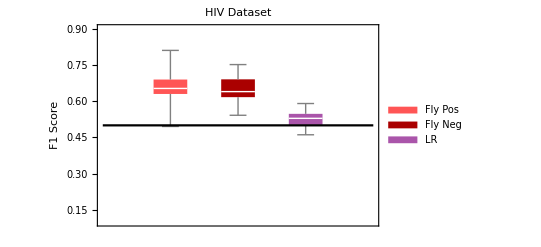

```mathematica
Show[F1HIVNeg,horiz]
```

Waiting for the model to run... seems to be substantially slower than the positive weights only model (wonder why?) Cancelled evaluation, running on smaller set
Above is the distribution of F1 scores, the new model is in the middle. I was only able to do 10 iterations of 100 test predictions rather than 20 iterations of 500 used in the other two, this may explain the tigether distribution? Regardless, there is a huge increase in evaluation time for some reason so in its current state this definitely is no feasible.

## Learned Weights (new Dasgupta model) *excluding this from my paper*

```mathematica
(*computes a single column, with the desired projection density*)
projectionDensity[m_Integer,sparsity_:0.1]:=With[
{samplingRate=Ceiling[m*sparsity]},
ConstantArray[1,samplingRate]~Join~ConstantArray[0,m-samplingRate]] 

(*creates the random high-dimensional representation, Θ, that projects an input in R^d into R^m by sampling the columns;
this should only be generated once per instance*)
sparseProjectionMatrix[d_Integer,m_Integer,sparsity_:0.1]:=With[
{column=projectionDensity[m,sparsity]},
Transpose@Table[RandomSample[column],d]
]

(*helper function to retain the largest l entries in an input vector*)
retainLargest[l_Integer][psi_?VectorQ]:=With[
{largestElements=ResourceFunction["PositionLargest"][psi,l],
allElements=Range@Length@psi},
ReplacePart[psi,Complement[allElements,largestElements]->0.]
]

(*implement the winner-take-all layer with MinMax rescaling, resulting in ϕ*)
winnerTakeAll[theta_?MatrixQ,l_Integer][x_?VectorQ]:=With[
{psi=theta.x},
Rescale@retainLargest[l]@psi]

(*define the incremental learning weight matrix*)
initializeWeights[m_Integer,k_Integer]:=ConstantArray[0.,{k,m}]

(*make a prediction about the largest output class; PositionLargest will default to the earliest entry if there are equal values*)
Clear[predict,predictPhi]
predictPhi[w_?MatrixQ][phi_?VectorQ]:=ResourceFunction["PositionLargest"][w.phi]

predict[theta_,l_,w_][x_]:=predictPhi[w]@winnerTakeAll[theta,l]@x

(*incremental learning rule ; in practice they don't include any forgetting so simplify this to save a few arithmetic operations;
weights are bounded 0 to 1 *)
Clear[learn,learnPhi]
learnPhi[alpha_,beta_][phi_?VectorQ->target_Integer][w_?MatrixQ]:=With[
{j=target,
wForget = (1-alpha)*w
}, (*target outcome ; no prediction is needed,unlike perceptron*)
ReplacePart[wForget,j->Clip[wForget[[j]]+beta*phi]]]

(*learns one example*)
learn[theta_?MatrixQ,l_,alpha_,beta_][w_?MatrixQ,x_?VectorQ->target_Integer]:=With[
{phi=winnerTakeAll[theta,l]@x},
learnPhi[alpha,beta][phi->target][w]]

(*learns over a collection of examples*)
learn[theta_?MatrixQ,l_,alpha_,beta_][w_?MatrixQ,examples_List]:=Fold[
learn[theta,l,alpha,beta],w,examples]


accuracy[theta_,l_,w_][examples_]:=With[
{predictions=predict[theta,l,w]/@examples[[All,1]],
true=examples[[All,2]]},
N@Mean@Boole@(Equal@@@Transpose[{predictions,true}])]
```

```mathematica
(* evaluate run time *)
d=2;
m=40*d;
k=2;
l=Ceiling[m/k];
alpha=.01;
beta=.01;

makeData[d_]:=Join[(#->1)&/@RandomInteger[{1,10},{100,d}],(#->2)&/@RandomInteger[{11,20},{100,d}]];

RunTime[d_]:=Module[
{m=40*d,
k=2,
l=Ceiling[m/k],
alpha=.01,
beta=.01,w0,w,theta},
SeedRandom[1841];
theta=sparseProjectionMatrix[d,m];
w0=initializeWeights[m,k];
w=learn[theta,l,alpha,beta][w0,makeData[d]];
Timing[accuracy[theta,l,w]@makeData[d]]];
```

```mathematica
times=Table[RunTime[x],{x,100,1000,100}];
```

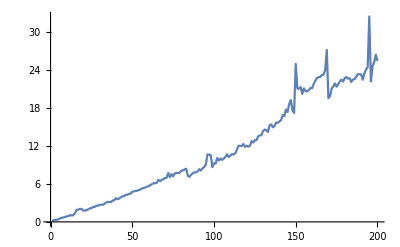

```mathematica
plot=ListLinePlot[Table[times[[x,1]],{x,1,Length[times]}]]
```

### Introducing negative weights

2 changes: 
- sparse projection matrix now contains +/-1
-winner take all function now extracts largest magnitude values (+/-)

```mathematica
Clear[projectionDensity,winnerTakeAll,times,plot];
projectionDensity[m_Integer,sparsity_:0.1]:=With[
{samplingRate=Ceiling[m*sparsity]},
ConstantArray[1,samplingRate/2]~Join~ConstantArray[-1,samplingRate/2]~Join~ConstantArray[0,m-samplingRate]];
winnerTakeAll[theta_?MatrixQ,l_Integer][x_?VectorQ]:=With[
{psi=Abs[theta.x]},
Rescale@retainLargest[l]@psi]
```

```mathematica
RunTime[100]
```

{1.48438,0.5}

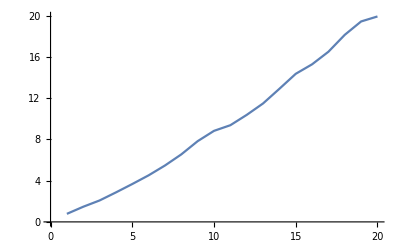

```mathematica
(* similar run time to the traditional model, not unreasonably slow *)
times=Table[RunTime[x],{x,100,1000,100}];
plot=ListLinePlot[Table[times[[x,1]],{x,1,Length[times]}]]
```

```mathematica
(* similar linear behavior as traditional sparse projection matrix *)
```

### Normally distributed sparse projection matrix

Similar changes as above,  projection matrix populated with values from N(0,1)

```mathematica
Clear[projectionDensity,times,plot];
projectionDensity[m_Integer,sparsity_:0.1]:=With[
{samplingRate=Ceiling[m*sparsity]},
RandomVariate[NormalDistribution[],samplingRate]~Join~ConstantArray[0,m-samplingRate]]
```

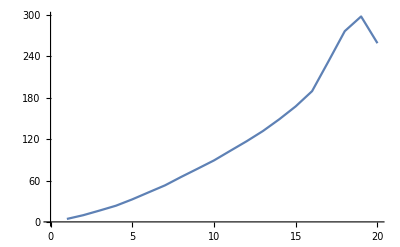

```mathematica
(* noticably greater penalties to time with a normally distributed sparse projection network... *)
times=Table[RunTime[x],{x,100,1000,100}];
plot=ListLinePlot[Table[times[[x,1]],{x,1,Length[times]}]]
```

```mathematica
(* seems to begin exponentially increasing time demands with higher dimensions *)
```

### Mu data (with +/-1 projection matrix)

```mathematica
Clear[projectionDensity,winnerTakeAll,times,plot];
projectionDensity[m_Integer,sparsity_:0.1]:=With[
{samplingRate=Ceiling[m*sparsity]},
ConstantArray[1,samplingRate/2]~Join~ConstantArray[-1,samplingRate/2]~Join~ConstantArray[0,m-samplingRate]];
winnerTakeAll[theta_?MatrixQ,l_Integer][x_?VectorQ]:=With[
{psi=Abs[theta.x]},
Rescale@retainLargest[l]@psi]
```

```mathematica
d=2048;
m=40*d;
k=2;
l=Ceiling[m/k];
alpha=.01;
beta=.01;

SeedRandom[1840];
theta=sparseProjectionMatrix[d,m];
w0=initializeWeights[m,k];
```

#### HIV

```mathematica
hivData=Join[(#->1)&/@actHIV,(#->2)&/@inactHIV];
shuffleHIVData=RandomSample[hivData];
initialHIVTrain=shuffleHIVData[[1;;100]];
initialHIVTest=shuffleHIVData[[101;;200]];
```

```mathematica
w=learn[theta,l,alpha,beta][w0,initialHIVTrain];
accuracy[theta,l,w]@initialHIVTest
accuracy[theta,l,w]@initialHIVTrain
```

0.51

0.51

```mathematica
predHIV=predict[theta,l,w]/@initialHIVTest[[All,1]];
predHIV[[1;;100]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Compare with Logistic Regression

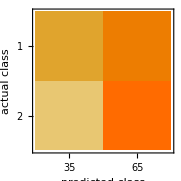
{0.54,-Graphics-}

```mathematica
ClassifierMeasurements[
Classify[initialHIVTrain,Method->"LogisticRegression"],
initialHIVTest,
{"Accuracy","ConfusionMatrixPlot"}]
```

#### Mu

```mathematica
muData=Join[(#->1)&/@actMu[[1;;788]],(#->2)&/@inactMu];
shuffleMuData=RandomSample[muData];
initialMuTrain=shuffleMuData[[1;;100]];
initialMuTest=shuffleMuData[[101;;200]];
```

```mathematica
w=learn[theta,l,alpha,beta][w0,initialMuTrain];
accuracy[theta,l,w]@initialMuTest
accuracy[theta,l,w]@initialMuTrain
```

0.56

0.52

```mathematica
predMu=predict[theta,l,w]/@initialMuTest[[All,1]];
predMu[[1;;100]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

Compare with Logistic Regression

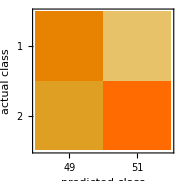
{0.61,-Graphics-}

```mathematica
ClassifierMeasurements[
Classify[initialMuTrain,Method->"LogisticRegression"],
initialMuTest,
{"Accuracy","ConfusionMatrixPlot"}]
```

#### Tox

```mathematica
toxData=Join[(#->1)&/@tox,(#->2)&/@nontox[[1;;310]]];
shuffleToxData=RandomSample[toxData];
initialToxTrain=shuffleToxData[[1;;100]];
initialToxTest=shuffleToxData[[101;;200]];
```

```mathematica
w=learn[theta,l,alpha,beta][w0,initialToxTrain];
accuracy[theta,l,w]@initialToxTest
accuracy[theta,l,w]@initialToxTrain
```

0.48

0.6

```mathematica
predTox=predict[theta,l,w]/@initialToxTest[[All,1]];
predTox[[1;;100]]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

Compare with Logistic Regression

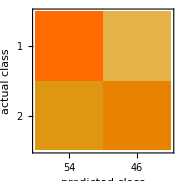
{0.56,-Graphics-}

```mathematica
ClassifierMeasurements[
Classify[initialToxTrain,Method->"LogisticRegression"],
initialToxTest,
{"Accuracy","ConfusionMatrixPlot"}]
```

Still predicts the majority class every time... introducing negative weights did not seem to solve the issue. Working on more steps forward